## 2.1a)

-1

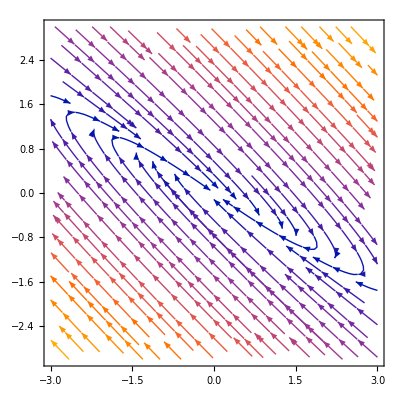

```mathematica
sigma=-1
StreamPlot[{(sigma+3)x+4y,(-9/4)x+(sigma-3)y},{x,-3,3},{y,-3,3}]
```

This is a stabel fixed point at (0,0)

0

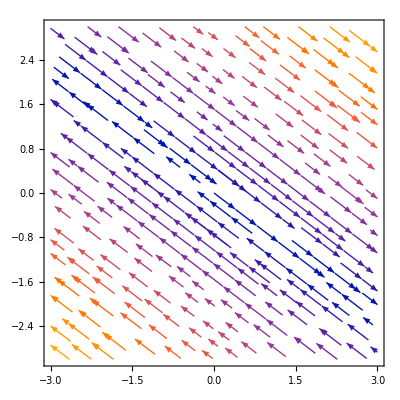

```mathematica
sigma=0
StreamPlot[{(sigma+3)x+4y,(-9/4)x+(sigma-3)y},{x,-3,3},{y,-3,3}]
```

This is a sadelpoint ? at (0,0)

1

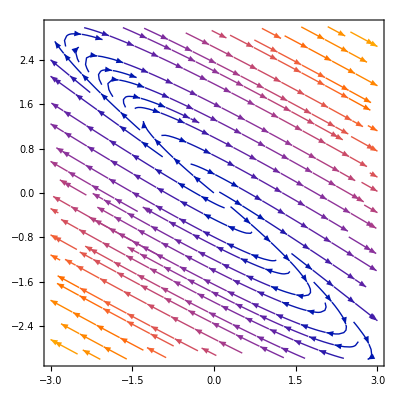

```mathematica
sigma=1
StreamPlot[{(sigma+3)x+4y,(-9/4)x+(sigma-3)y},{x,-3,3},{y,-3,3}]
```

This is a unstable fixed point at (0,0)

## 2.1 b)

```mathematica
matrix={{σ+3,4},{-9/4,σ-3}}
```

```mathematica
matrix={{σ+3,4},{-9/4,σ-3}};
```

2.1c)

```mathematica
vectors=Eigenvectors[{{3+σ,4},{-9/4,-3+σ}}]
```

{{-4/3,1},{0,0}}

```mathematica
eigenVector=vectors[[1]]
```

{-4/3,1}

```mathematica
magnitude=Sqrt[Total[eigenVector^2]];
```

```mathematica
normalizedVector=-eigenVector/magnitude
```

{4/5,-3/5}

2.1 d)

```mathematica
Inverse[matrix]
```

{{(-12+4 σ)/(4 σ^2),-4/σ^2},{9/(4 σ^2),(3+σ)/σ^2}}

12.1 e)
when sigma =0 inverse of A goes to inf therfor sigma =0 implies that invers of A dosent excist in this particular case (sigma =0)

2.1 f)

```mathematica
matrixGeneral={{σ-cd,d^2},{-c^2,σ+cd}}
matrixSigmaMinus={{-1-cd,d^2},{-c^2,-1+cd}}
```

{{-cd+σ,d^2},{-c^2,cd+σ}}

{{-1-cd,d^2},{-c^2,-1+cd}}

```mathematica
Eigensystem[matrixSigmaMinus]
```

{{-1-√(cd^2-c^2 d^2),-1+√(cd^2-c^2 d^2)},{{-(-cd-√(cd^2-c^2 d^2))/c^2,1},{-(-cd+√(cd^2-c^2 d^2))/c^2,1}}}

```mathematica
Eigenvalues[matrixSigmaMinus]
```

{-1-√(cd^2-c^2 d^2),-1+√(cd^2-c^2 d^2)}

```mathematica
Eigenvectors[matrixSigmaMinus]
```

{{-(-cd-√(cd^2-c^2 d^2))/c^2,1},{-(-cd+√(cd^2-c^2 d^2))/c^2,1}}

Eigenvalues should be the same as previous [sigma,sigma] (sigma=-1) therfore sqrt(cd^2-c^2d^2)=0 . Given this the eigenvector is [d/c,1].